Recursively evaluating some low values of C(n_1,n_0).
We make use of equations 1, 2, 3, and 4.

```mathematica
c00=(Cosh[γ])^(-1/2);
```

```mathematica
(* Evaluating Eq. 1 with n0 = 1 *)
c11=(Cosh[γ])^-1 c00 ;
```

```mathematica
(* Evaluating Eq. 3 with n0 = 1 *)
c02=Simplify[2^(-1/2)(-Sinh[γ])c11 ];
```

```mathematica
(* Evaluating Eq. 1 with n0 = 3 *)
c13=Simplify[(Cosh[γ])^-1 c02 3^(1/2)];
```

```mathematica
(* Evaluating Eq. 2 with n0 = 2 and n1 = 1 *)
c22a=Simplify[(Cosh[γ] 2^(1/2))^-1(c11 2^(1/2)+c02 Sinh[γ])];
```

```mathematica
(* Evaluating Eq. 4 with n0 = 2 and n1 = 1 *)
c22b=Simplify[(-Sinh[γ] 2^(1/2))^-1(c13 3^(1/2)-c02 Cosh[γ])];
```

```mathematica
c22=c22b;
```

```mathematica
(* Evaluating Eq. 3 with n0 = 3 *)
c04=Simplify[4^(-1/2)(-Sinh[γ])c13];
```

```mathematica
(* Evaluating Eq. 1 with n0 = 5 *)
c15=Simplify[Cosh[γ]^-1 c04 5^(1/2)];
```

```mathematica
(* Evaluating Eq. 2 with n0 = 4 and n1 = 1 *)
c24a=Simplify[(Cosh[γ] 2^(1/2))^-1(c13 4^(1/2)+c04 Sinh[γ])];
```

```mathematica
(* Evaluating Eq. 4 with n0 = 4 and n1 = 1 *)
c24b = Simplify[(Sinh[γ] 2^(1/2))^-1(c04 Cosh[γ]-c15 5^(1/2))];
```

```mathematica
c24=c24a;
```

```mathematica
(* Evaluating Eq. 4 with n0 = 0 and n1 = 1 *)
c20=Simplify[(Sinh[γ] 2^(1/2))^-1(c00 Cosh[γ]-c11)];
```

Miscellaneous
Some calculations for solving the PDE of F(x,y)

```mathematica
p=((x+1)(y-1))/((x-1)(y+1));
```

```mathematica
Simplify[1/Cosh[γ](((p+1)^2-Tanh[γ]^2(p-1)^2)/(4p))^(-1/2) ,Assumptions->x>0&&x<1&&y>0&&y<1]
```

(√((-1+x^2) (-1+y^2)) Sech[γ])/(√((-1+x y)^2-(x-y)^2 Tanh[γ]^2))

Calculating the first 100 values of D(n_1,n_0)
F(x,y) is found in equation 12, and the form for D(n_1,n_0) is given in equation 13.  The 100 values determined below were used to generate Table 1.

```mathematica
F[x_,y_]:=((x y-1)^2 Cosh[γ]^2-(x-y)^2 Sinh[γ]^2)^(-1/2);
```

```mathematica
d[n1_,n0_]:=Simplify[1/(n1!n0!)D[F[x,y],{x,n1},{y,n0}]/.x->0/.y->0,Assumptions->γ>0]
```

```mathematica
N[Table[d[n1,n0],{n1,0,9},{n0,0,9}]/.γ->1,2]
```

{{0.65,0,0.19,0,0.082,0,0.04,0,0.02,0},{0,0.27,0,0.24,0,0.17,0,0.12,0,0.076},{0.19,0,0.011,0,0.085,0,0.13,0,0.13,0},{0,0.24,0,0.055,0,0.00018,0,0.02,0,0.057},{0.082,0,0.085,0,0.12,0,0.061,0,0.012,0},{0,0.17,0,0.00018,0,0.046,0,0.082,0,0.067},{0.04,0,0.13,0,0.061,0,0.0011,0,0.019,0},{0,0.12,0,0.02,0,0.082,0,0.05,0,0.0067},{0.02,0,0.13,0,0.012,0,0.019,0,0.059,0},{0,0.076,0,0.057,0,0.067,0,0.0067,0,0.0097}}

Showing visually the first 21 D(n,n)

```mathematica
nk=Table[d[n,n],{n,0,20}];
```

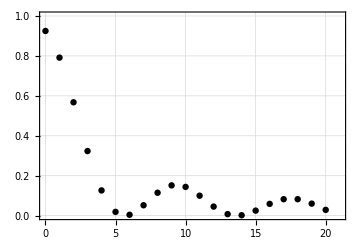

```mathematica
p=ListPlot[Table[{n-1,nk[[n]]},{n,1,21}]/.γ->0.4,PlotRange->{{0,21},{0,1}},Frame->True, GridLines->Automatic,PlotStyle->Black,AxesStyle->{Black},AspectRatio->2/3,ImageSize->Medium];
Show[p]
```